```mathematica
ClearAll[x,y,z,flukaData,flukaDataIP]
```

```mathematica
flukaData=Import["/home/hovanes/powerDensityKPT.csv","CSV"];
```

```mathematica
flukaDataIP=Interpolation[flukaData]
```

InterpolatingFunction[{{20.375, 80.375}, {0.5, 10.5}}, <>]

```mathematica
Export["/home/hovanes/Documents/Wolfram Mathematica/CPS_Temperature_With_Mathematica/kptPower.m" , flukaDataIP]
```

/home/hovanes/Documents/Wolfram Mathematica/CPS_Temperature_With_Mathematica/kptPower.m

InterpolatingFunction::dmval: Input value {60.0009,0.000714286} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {61.0714,0.178571} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {61.2857,0.357143} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

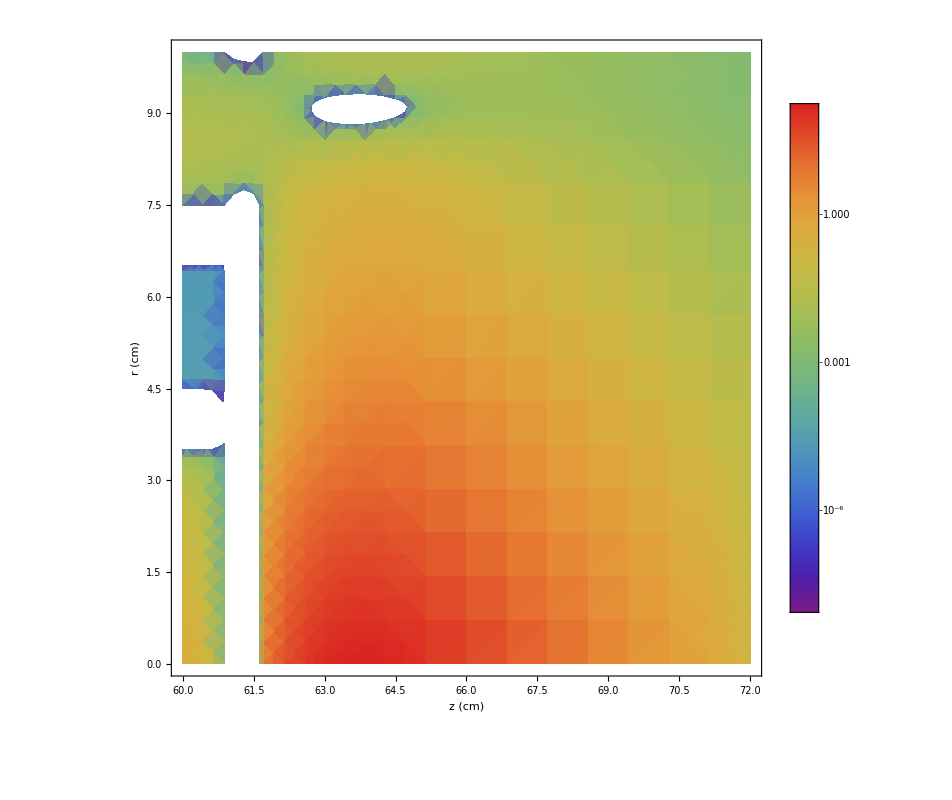

```mathematica
DensityPlot[flukaDataIP[z,r],{z, 60, 72},{r,0, 10 },ColorFunction->{"Rainbow"},PlotRange->Full,PlotLegends->Automatic, ScalingFunctions->{Identity,Identity,"Log"},ImageSize->{800,800},FrameLabel->{"z (cm)", "r (cm)", "ΔP/ΔV (W/SuperscriptBox[cm, 3] )"} , LabelStyle->{22,GrayLevel[0],Italic},AspectRatio->1]
```